## K-states representation for the wave functions |IMK>

## Constants

```mathematica
angles={π/3,π/5,π/7};
spin=3;
```

## Wigner functions

```mathematica
wd[spin_,m_,k_,angles_]:=WignerD[{spin,m,k},angles[[1]],angles[[2]],angles[[3]]];
wdreal[spin_,m_,k_,angles_]:=Re[wd[spin,m,k,angles]];
```

```mathematica
Kstates[spin_,k_,angles_]:=Table[N[wdreal[spin,mi,k,angles]],{mi,-spin,spin,1}];
```

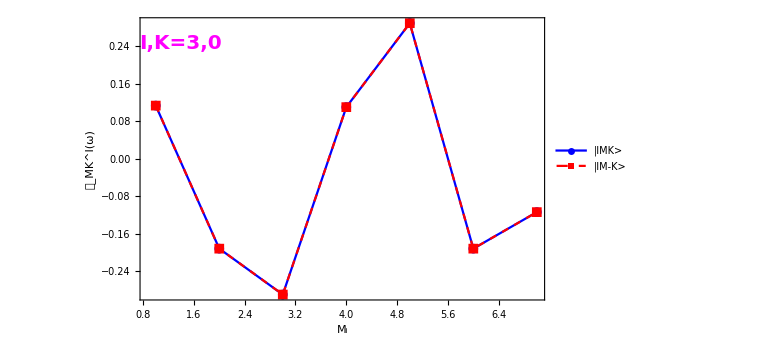
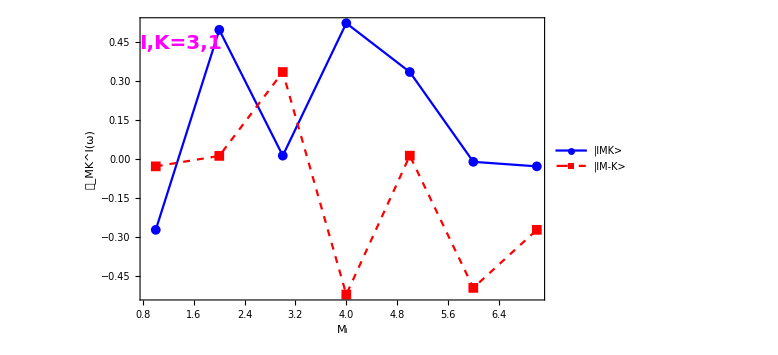
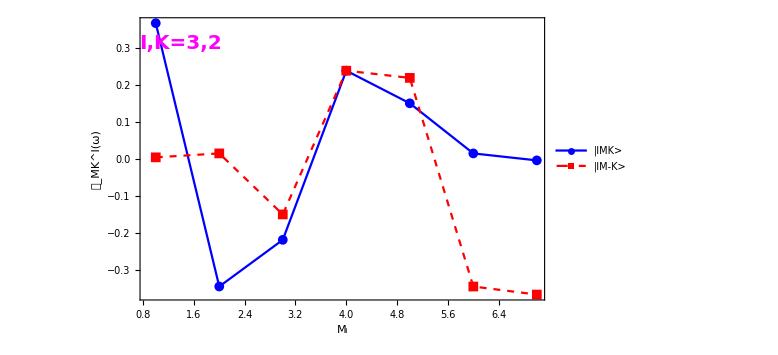
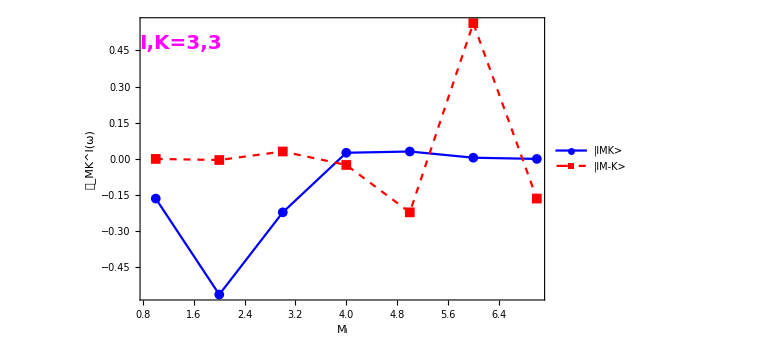
-Graphics- | -Graphics-
-Graphics- | -Graphics-

```mathematica
pairplot[spin_,k_,angles_]:=ListPlot[{Kstates[spin,-k,angles],Kstates[spin,k,angles]},Joined->True,PlotMarkers->{Automatic, Medium},Frame->True,PlotRange->All,PlotStyle->{{Blue},{Red,Dashed}},FrameStyle->Directive[Black,Thick],FrameLabel->{"M_i","𝒟_MK^I(ω)"},LabelStyle->{18,Black,Bold,FontFamily->"Times"},ImageSize->Large,PlotLegends->{"|IMK>","|IM-K>"},Epilog->Inset[Style[StringTemplate["I,K=``,``"][spin,k],20,Bold,Magenta,Italic],Scaled[{0.1,0.91}]]];
Grid[{{pairplot[3,0,angles],pairplot[3,1,angles]},{pairplot[3,2,angles],pairplot[3,3,angles]}}]
```